#### Calculating Spinor Coefficients C_i

Here I implement a way to calculate the spinor coefficients denoted C_i for an arbitrary number of particles with arbitrary spin

The function Coeff will attempt to calculate the desired coefficient analytically -- this works for two spin 1/2 particles and for three spin 1/2 particles
After that, the integrals are very slow to solve

NCoeff attempts to calculate C_i by numerically solving the integrals in the Coeff function. This is quite a bit faster but still gets slow after 4 or so particles

LDACoeff calculates the coefficients using the local density approximation. This is very fast even for large numbers of particles and usually has an error on the order of  10^-1 or 10^-2

```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
A[n_] = 2^((n-1)n/4)/(π^(n/4)*Sqrt[Product[Factorial[j],{j,0,n}]]);
(* W is a sequence (not a list) of the variables --- e.g., Subscript[ψ, F][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]] *)
Subscript[ψ, F][W__]:= Module[{prod,i},
prod=1;
For[i=1,i<Length[{W}],i++,prod = prod*Product[({W}[[j]]-{W}[[i]]),{j, i + 1,Length[{W}]}]];
A[Length[{W}]]*Exp[-1/2 Sum[({W}[[j]])^2,{j,1,Length[{W}]}]]*prod];
(* i denotes the desired coefficient where 1 ≤ i ≤ N - 1 and n denotes the number of particles N *)
Coeff[i_,n_] :=  Module[{X,θ,Κ,j},
X = Table[Subscript[x, j],{j,1,n}];
θ=Product[If[ j!=i , HeavisideTheta[Subscript[x, j+1]-Subscript[x, j]],1],{j,1,n-1}];
Κ=Integrate[FullSimplify[D[Subscript[ψ, F]@@X,Subscript[x, i]]^2]*DiracDelta[Subscript[x, i+1]-Subscript[x, i]]*θ,{Subscript[x, i],-Infinity, Infinity}];
For[j=1,j≤n,j++, If[j≠i,Κ=Integrate[Κ,{Subscript[x, j],-Infinity, Infinity}],1]];
Factorial[n]*Κ]
NCoeff[i_,n_] :=NCoeff[i,n]= Module[{X,θ,Κ,j,vars},
X = Table[Subscript[x, j],{j,1,n}];
θ=Product[If[ j!=i , HeavisideTheta[Subscript[x, j+1]-Subscript[x, j]],1],{j,1,n-1}];
Κ=Integrate[FullSimplify[D[Subscript[ψ, F]@@X,Subscript[x, i]]^2]*DiracDelta[Subscript[x, i+1]-Subscript[x, i]]*θ,{Subscript[x, i],-Infinity, Infinity},GenerateConditions->False];
vars=Delete[Table[Subscript[x, j],{j,1,n}],i];
Κ=NIntegrate[Κ,##]&@@({#,-∞,∞}&/@vars);
Factorial[n]*Κ]
(* This gives the local density approximation for the coefficients. Error is noticeable for N ≤ 3 but is otherwise quite good *)
LDACoeff[i_,n_]:= Block[{x,y},
x=y/.NSolve[y-2 π i/n==Sin[y]&&Im[y]==0,y][[1]];
N[1/(3π)(2*n)^(3/2)Sin[x/2]^3]]
```

#### Spin Chain Hamiltonian ℋ_sc

Here I calculate the spin chain Hamiltonian with spin dependent interaction for arbitrary number of particles (bosons or fermions) with arbitrary spin

Statevector function calculates every possible spin state in the single particle spin basis (i.e., the |s_1,m_1; s_2, m_2 ⟩  basis if it were two particles)

```mathematica
(* This function constructs our "statevector" where n is the number of particles and s is the spin, e.g., s = 1/2, 1, 3/2,... *)
StateVector[n_,s_]:= Reverse[Table[Join[Table[0,{i,1,n - Floor[Log[1+2s,If[i==0,1,i]]]-1}],IntegerDigits[i,1+2s]],{i, 0,(1+2s)^n-1}]]-s
(* Takes as input two basis elements -- i.e., a single element from matrix output of the StateVector function -- e.g., {1,0} and {0,1}. Returns 1 if state vectors are the same, 0 otherwise *)
InnerProduct[u_,v_]:=Product[Boole[u[[i]]==v[[i]]],{i,1,Length[u]}];
(* Takes bra vector u as input and performs exchange on i^th element *)
Exchange[v_,i_]:=Module[{u,t},
u=v;t = u[[i]];
u[[i]]=u[[i+1]];
u[[i+1]]=t;u]
(* This returns the exchange matrix Subscript[E, i, i+1] for a given number of particles n, an index i, and a spin s *)
𝔼[n_,i_,s_]:= Module[{𝒮},
𝒮=StateVector[n,s];
Table[InnerProduct[𝒮[[j]],Exchange[𝒮[[k]], i]],{j,1,(1+2s)^n},{k,1,(1+2s)^n}]]
(* This creates the symmetry/antisymmetry projection operator using 𝔼. Arguments represent the same things as before but now b is 1 for bosons and 0 for fermions *)
𝒫[n_,i_,s_,b_]:=IdentityMatrix[(1+2s)^n]-(-1)^b 𝔼[n,i,s];
```

Now I will create function that will project a state in the single spin basis onto the total spin basis 
ReduceStateVector[u, M] takes an output u from StateVector[n,s] and removes all basis elements that don’t have total S_z spin equal to M -- this will help simplify the Hamiltonian we need to diagonalize
TotalSpin[J, M,s ] expresses the total spin state for |J, M ⟩ in the single spin basis for two particles with spin s
TotalSpinSubProjection[J,M,s] expresses the projection operator for the Total Spin State |J,M> as a matrix --> |J,M><J,M| uing just the single particle basis states of the two particles involved
TotalSpinProjection[J,M,s,i,n] creates the projection matrix as it would be expressed using the single particle basis state for all n particles

```mathematica
ReduceStateVector[n_,s_, M_] := Part[StateVector[n,s],Flatten[Position[Table[Sum[StateVector[n,s][[k]][[ℓ]],{ℓ,1,n}]==M,{k,1,(1+2s)^n}],True]]];
TotalSpin[J_,M_,s_]:= Module[{𝒮},
𝒮=StateVector[2, s];
Table[ClebschGordan[{s,𝒮[[i]][[1]]},{s,𝒮[[i]][[2]]},{J, M}],{i, 1,Length[𝒮]}]]//Quiet
TotalSpinSubProjection[J_,M_,s_]:=Transpose[{TotalSpin[J,M,s]}].{TotalSpin[J,M,s]}
TotalSpinProjection[J_,M_,s_,i_,n_]:= Apply[TensorProduct,Delete[Table[If[i == j, TotalSpinSubProjection[J,M,s],If[j≠i+1,IdentityMatrix[(1+2s)]]],{j,1,n}],i+1]]//ArrayFlatten;
```

To start off, we will construct the spin-dependent spin-chain hamiltonian for particles with spin -1
For the three particle case, we can eliminate some variables to simplify our problem
We can eliminate C_i because they are the same for three particles
And we can rescale our Hamiltonian by g_2 and work only with G = g_2 /  g_0

```mathematica
(*Subscript[H, sc][n_, b_]:=Sum[Subscript[C, i](1/Subscript[g, 0]*𝒫[n,i,1,b].TotalSpinProjection[0,0,1,i,n] + 
1/Subscript[g, 2]Sum[𝒫[n,i,1,b].TotalSpinProjection[2,M,1,i,n],{M,-2,2}]),{i,1,n-1}];*)
Subscript[H, sc][n_, b_]:=Sum[(G*𝒫[n,i,1,b].TotalSpinProjection[0,0,1,i,n] + 
Sum[𝒫[n,i,1,b].TotalSpinProjection[2,M,1,i,n],{M,-2,2}]),{i,1,n-1}];
```

For now we are only interested in eigenstates that have S_z = 0, so we can delete rows and columns from H_sc that don’t satisfy that constraint

```mathematica
ReduceH[n_,s_,b_,m_]:=Module[{I},I=Position[Table[Sum[StateVector[n,s][[k]][[ℓ]],{ℓ,1,n}]==m,{k,1,(1+2s)^n}],False];Delete[Transpose[Delete[Transpose[Subscript[H, sc][n,b]],I]],I]]
```

```mathematica
n=3;
i=1;
s=1;
𝒫[n,i,s,1]//Dimensions
TotalSpinProjection[2,0,s,i,n]//Dimensions
Flatten[TotalSpinProjection[2,0,s,i,n],1]//MatrixForm;
Partition[Flatten[TotalSpinProjection[2,0,s,i,n],5],27]//MatrixForm;
```

{27,27}

{27,27}

```mathematica
Array[a,{2,2,2,2,2}]//Dimensions
ArrayFlatten[Array[a,{2,2,2,2,2}],2]//Dimensions
```

```mathematica
StateVector[3,1]//MatrixForm
Subscript[H, sc][3,1]//MatrixForm;
Eigensystem[Subscript[H, sc][3,1]]//Transpose//MatrixForm
```

```mathematica
A=RandomInteger[9,{6,4}];
A//MatrixForm
A[[All, 2;;]]//MatrixForm
```

(0 | 3 | 0 | 7
7 | 0 | 9 | 5
6 | 6 | 0 | 5
7 | 5 | 9 | 6
0 | 4 | 1 | 1
4 | 2 | 5 | 9)

(3 | 0 | 7
0 | 9 | 5
6 | 0 | 5
5 | 9 | 6
4 | 1 | 1
2 | 5 | 9)

```mathematica
n=3;
i=1;
s=1;
ReduceStateVector[n,s,0]//MatrixForm
Subscript[H, sc][n,s]//MatrixForm;
ReduceH[n,s,1,0]//Eigensystem//Transpose//MatrixForm
```

(1 | 0 | -1
1 | -1 | 0
0 | 1 | -1
0 | 0 | 0
0 | -1 | 1
-1 | 1 | 0
-1 | 0 | 1)

(0 | {-1,1,1,0,-1,-1,1}
Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]/(1594323 g_0^13 g_2^13) | {-(Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^6-7971615 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^5 C_1 g_0^13 g_2^12-7971615 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^5 C_2 g_0^13 g_2^12-3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^5 C_1 g_0^12 g_2^13-3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^5 C_2 g_0^12 g_2^13+20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_1^2 g_0^26 g_2^24+53096752858428 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_1 C_2 g_0^26 g_2^24+20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_2^2 g_0^26 g_2^24+25418658283290 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_1^2 g_0^25 g_2^25+39540135107340 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_1 C_2 g_0^25 g_2^25+25418658283290 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_2^2 g_0^25 g_2^25+9037745167392 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_1 C_2 g_0^24 g_2^26-16210220612075905068 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1^3 g_0^39 g_2^36-110769840849185351298 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1^2 C_2 g_0^39 g_2^36-110769840849185351298 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 C_2^2 g_0^39 g_2^36-16210220612075905068 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2^3 g_0^39 g_2^36-64840882448303620272 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1^3 g_0^38 g_2^37-159400502685413066502 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1^2 C_2 g_0^38 g_2^37-159400502685413066502 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 C_2^2 g_0^38 g_2^37-64840882448303620272 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2^3 g_0^38 g_2^37-54034068706919683560 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1^2 C_2 g_0^37 g_2^38-54034068706919683560 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 C_2^2 g_0^37 g_2^38+71789798769185258877024900 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^3 C_2 g_0^52 g_2^48+174449211009120179071170507 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 C_2^2 g_0^52 g_2^48+71789798769185258877024900 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2^3 g_0^52 g_2^48+51688655113813386391457928 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^4 g_0^51 g_2^49+252700091667532111247127648 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^3 C_2 g_0^51 g_2^49+344591034092089242609719520 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 C_2^2 g_0^51 g_2^49+252700091667532111247127648 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2^3 g_0^51 g_2^49+51688655113813386391457928 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^4 g_0^51 g_2^49+89019350473789721007510876 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^3 C_2 g_0^50 g_2^50+223984172159858007696317688 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 C_2^2 g_0^50 g_2^50+89019350473789721007510876 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2^3 g_0^50 g_2^50-74396482773004437167586730267755 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 C_2^2 g_0^65 g_2^60-74396482773004437167586730267755 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2^3 g_0^65 g_2^60-137347352811700499386313963571240 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^4 C_2 g_0^64 g_2^61-283851195810847698731715524713896 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 C_2^2 g_0^64 g_2^61-283851195810847698731715524713896 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2^3 g_0^64 g_2^61-137347352811700499386313963571240 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^4 g_0^64 g_2^61-27469470562340099877262792714248 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^4 C_2 g_0^63 g_2^62-228912254686167498977189939285400 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 C_2^2 g_0^63 g_2^62-228912254686167498977189939285400 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2^3 g_0^63 g_2^62-27469470562340099877262792714248 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^4 g_0^63 g_2^62+54744010894202193820771559335697517630 C_1^4 C_2^2 g_0^77 g_2^73+109488021788404387641543118671395035260 C_1^3 C_2^3 g_0^77 g_2^73+54744010894202193820771559335697517630 C_1^2 C_2^4 g_0^77 g_2^73+43795208715361755056617247468558014104 C_1^4 C_2^2 g_0^76 g_2^74+87590417430723510113234494937116028208 C_1^3 C_2^3 g_0^76 g_2^74+43795208715361755056617247468558014104 C_1^2 C_2^4 g_0^76 g_2^74)/(1350851717672992089 C_1 C_2 g_0^38 g_2^36 (-Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0-Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_2-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_2+3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^14 g_2^12+2125764 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^14 g_2^12+3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^14 g_2^12+9565938 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^13 g_2^13+40389516 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^13 g_2^13+9565938 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^13 g_2^13+6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^12 g_2^14-4251528 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^12 g_2^14+6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^12 g_2^14-4236443047215 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^27 g_2^24-4236443047215 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^27 g_2^24-10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^26 g_2^25-83034283725414 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^26 g_2^25-83034283725414 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^26 g_2^25-10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^26 g_2^25-20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^25 g_2^26-27113235502176 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^25 g_2^26-27113235502176 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^25 g_2^26-20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^25 g_2^26+40525551530189762670 C_1^3 C_2 g_0^39 g_2^37+81051103060379525340 C_1^2 C_2^2 g_0^39 g_2^37+40525551530189762670 C_1 C_2^3 g_0^39 g_2^37+32420441224151810136 C_1^3 C_2 g_0^38 g_2^38+64840882448303620272 C_1^2 C_2^2 g_0^38 g_2^38+32420441224151810136 C_1 C_2^3 g_0^38 g_2^38)),-(Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^5-7440174 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_1 g_0^13 g_2^12-6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_2 g_0^13 g_2^12-2125764 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_1 g_0^12 g_2^13-3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_2 g_0^12 g_2^13+18922778944227 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1^2 g_0^26 g_2^24+37845557888454 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 C_2 g_0^26 g_2^24+10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2^2 g_0^26 g_2^24+12991758678126 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1^2 g_0^25 g_2^25+27678094575138 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 C_2 g_0^25 g_2^25+20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2^2 g_0^25 g_2^25+1129718145924 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1^2 g_0^24 g_2^26+5648590729620 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 C_2 g_0^24 g_2^26-17110788423857899794 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^3 g_0^39 g_2^36-72045424942559578080 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 C_2 g_0^39 g_2^36-45028390589099736300 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2^2 g_0^39 g_2^36-27917602165241836506 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^3 g_0^38 g_2^37-72045424942559578080 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 C_2 g_0^38 g_2^37-93659052425327451504 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2^2 g_0^38 g_2^37-32420441224151810136 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^3 g_0^38 g_2^37-3602271247127978904 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^3 g_0^37 g_2^38-34221576847715799588 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 C_2 g_0^37 g_2^38-23414763106331862876 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2^2 g_0^37 g_2^38+46663369199970418270066185 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 C_2 g_0^52 g_2^48+46663369199970418270066185 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2^2 g_0^52 g_2^48+25844327556906693195728964 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^4 g_0^51 g_2^49+70354002793801553699484402 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 C_2 g_0^51 g_2^49+130657433759917171156185318 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2^2 g_0^51 g_2^49+86147758523022310652429880 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^3 g_0^51 g_2^49+57431839015348207101619920 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 C_2 g_0^50 g_2^50+74661390719952669232105896 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2^2 g_0^50 g_2^50+17229551704604462130485976 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^3 g_0^50 g_2^50-34336838202925124846578490892810 C_1^4 C_2 g_0^64 g_2^61-68673676405850249693156981785620 C_1^3 C_2^2 g_0^64 g_2^61-34336838202925124846578490892810 C_1^2 C_2^3 g_0^64 g_2^61-27469470562340099877262792714248 C_1^4 C_2 g_0^63 g_2^62-54938941124680199754525585428496 C_1^3 C_2^2 g_0^63 g_2^62-27469470562340099877262792714248 C_1^2 C_2^3 g_0^63 g_2^62)/(847288609443 C_1 g_0^25 g_2^24 (-Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0-Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_2-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_2+3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^14 g_2^12+2125764 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^14 g_2^12+3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^14 g_2^12+9565938 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^13 g_2^13+40389516 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^13 g_2^13+9565938 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^13 g_2^13+6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^12 g_2^14-4251528 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^12 g_2^14+6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^12 g_2^14-4236443047215 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^27 g_2^24-4236443047215 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^27 g_2^24-10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^26 g_2^25-83034283725414 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^26 g_2^25-83034283725414 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^26 g_2^25-10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^26 g_2^25-20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^25 g_2^26-27113235502176 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^25 g_2^26-27113235502176 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^25 g_2^26-20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^25 g_2^26+40525551530189762670 C_1^3 C_2 g_0^39 g_2^37+81051103060379525340 C_1^2 C_2^2 g_0^39 g_2^37+40525551530189762670 C_1 C_2^3 g_0^39 g_2^37+32420441224151810136 C_1^3 C_2 g_0^38 g_2^38+64840882448303620272 C_1^2 C_2^2 g_0^38 g_2^38+32420441224151810136 C_1 C_2^3 g_0^38 g_2^38)),-(Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^5-6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_1 g_0^13 g_2^12-7440174 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_2 g_0^13 g_2^12-3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_1 g_0^12 g_2^13-2125764 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 C_2 g_0^12 g_2^13+10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1^2 g_0^26 g_2^24+37845557888454 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 C_2 g_0^26 g_2^24+18922778944227 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2^2 g_0^26 g_2^24+20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1^2 g_0^25 g_2^25+27678094575138 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 C_2 g_0^25 g_2^25+12991758678126 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2^2 g_0^25 g_2^25+5648590729620 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 C_2 g_0^24 g_2^26+1129718145924 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2^2 g_0^24 g_2^26-45028390589099736300 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 C_2 g_0^39 g_2^36-72045424942559578080 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2^2 g_0^39 g_2^36-17110788423857899794 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^3 g_0^39 g_2^36-32420441224151810136 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^3 g_0^38 g_2^37-93659052425327451504 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 C_2 g_0^38 g_2^37-72045424942559578080 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2^2 g_0^38 g_2^37-27917602165241836506 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^3 g_0^38 g_2^37-23414763106331862876 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 C_2 g_0^37 g_2^38-34221576847715799588 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2^2 g_0^37 g_2^38-3602271247127978904 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^3 g_0^37 g_2^38+46663369199970418270066185 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2^2 g_0^52 g_2^48+46663369199970418270066185 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^3 g_0^52 g_2^48+86147758523022310652429880 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 C_2 g_0^51 g_2^49+130657433759917171156185318 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2^2 g_0^51 g_2^49+70354002793801553699484402 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^3 g_0^51 g_2^49+25844327556906693195728964 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^4 g_0^51 g_2^49+17229551704604462130485976 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 C_2 g_0^50 g_2^50+74661390719952669232105896 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2^2 g_0^50 g_2^50+57431839015348207101619920 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^3 g_0^50 g_2^50-34336838202925124846578490892810 C_1^3 C_2^2 g_0^64 g_2^61-68673676405850249693156981785620 C_1^2 C_2^3 g_0^64 g_2^61-34336838202925124846578490892810 C_1 C_2^4 g_0^64 g_2^61-27469470562340099877262792714248 C_1^3 C_2^2 g_0^63 g_2^62-54938941124680199754525585428496 C_1^2 C_2^3 g_0^63 g_2^62-27469470562340099877262792714248 C_1 C_2^4 g_0^63 g_2^62)/(847288609443 C_2 g_0^25 g_2^24 (-Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0-Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_2-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_2+3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^14 g_2^12+2125764 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^14 g_2^12+3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^14 g_2^12+9565938 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^13 g_2^13+40389516 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^13 g_2^13+9565938 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^13 g_2^13+6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^12 g_2^14-4251528 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^12 g_2^14+6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^12 g_2^14-4236443047215 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^27 g_2^24-4236443047215 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^27 g_2^24-10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^26 g_2^25-83034283725414 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^26 g_2^25-83034283725414 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^26 g_2^25-10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^26 g_2^25-20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^25 g_2^26-27113235502176 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^25 g_2^26-27113235502176 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^25 g_2^26-20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^25 g_2^26+40525551530189762670 C_1^3 C_2 g_0^39 g_2^37+81051103060379525340 C_1^2 C_2^2 g_0^39 g_2^37+40525551530189762670 C_1 C_2^3 g_0^39 g_2^37+32420441224151810136 C_1^3 C_2 g_0^38 g_2^38+64840882448303620272 C_1^2 C_2^2 g_0^38 g_2^38+32420441224151810136 C_1 C_2^3 g_0^38 g_2^38)),(2 (-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 g_0+2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 g_2+9034497 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0^14 g_2^12+9034497 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0^14 g_2^12-6908733 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0^13 g_2^13-6908733 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0^13 g_2^13-2125764 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0^12 g_2^14-2125764 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0^12 g_2^14-8472886094430 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^27 g_2^24-32196967158834 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^27 g_2^24-8472886094430 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^27 g_2^24+1694577218886 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^26 g_2^25+18640349407746 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^26 g_2^25+1694577218886 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^26 g_2^25+6778308875544 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^25 g_2^26+13556617751088 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^25 g_2^26+6778308875544 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^25 g_2^26+20262775765094881335 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^40 g_2^36+20262775765094881335 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^40 g_2^36-4052555153018976267 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^39 g_2^37-4052555153018976267 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^39 g_2^37-16210220612075905068 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^38 g_2^38-16210220612075905068 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^38 g_2^38))/(1594323 g_0^13 g_2^12 (-Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0-Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_2-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_2+3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^14 g_2^12+2125764 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^14 g_2^12+3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^14 g_2^12+9565938 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^13 g_2^13+40389516 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^13 g_2^13+9565938 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^13 g_2^13+6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^12 g_2^14-4251528 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^12 g_2^14+6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^12 g_2^14-4236443047215 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^27 g_2^24-4236443047215 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^27 g_2^24-10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^26 g_2^25-83034283725414 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^26 g_2^25-83034283725414 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^26 g_2^25-10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^26 g_2^25-20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^25 g_2^26-27113235502176 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^25 g_2^26-27113235502176 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^25 g_2^26-20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^25 g_2^26+40525551530189762670 C_1^3 C_2 g_0^39 g_2^37+81051103060379525340 C_1^2 C_2^2 g_0^39 g_2^37+40525551530189762670 C_1 C_2^3 g_0^39 g_2^37+32420441224151810136 C_1^3 C_2 g_0^38 g_2^38+64840882448303620272 C_1^2 C_2^2 g_0^38 g_2^38+32420441224151810136 C_1 C_2^3 g_0^38 g_2^38)),-(Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 g_0+2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 g_2-4782969 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0^14 g_2^12-2657205 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0^14 g_2^12-12754584 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0^13 g_2^13-23383404 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0^13 g_2^13-6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0^12 g_2^14+2125764 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0^12 g_2^14+5083731656658 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^27 g_2^24+14403906360531 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^27 g_2^24-1694577218886 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^27 g_2^24+25418658283290 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^26 g_2^25+93201747038730 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^26 g_2^25+69477665974326 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^26 g_2^25+30502389939948 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^25 g_2^26+37280698815492 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^25 g_2^26-6778308875544 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^25 g_2^26-6754258588364960445 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^40 g_2^36-6754258588364960445 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^40 g_2^36-16210220612075905068 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^39 g_2^37-140488578637991177256 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^39 g_2^37-172909019862142987392 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^39 g_2^37-48630661836227715204 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^39 g_2^37-32420441224151810136 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^38 g_2^38-108068137413839367120 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^38 g_2^38-75647696189687556984 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^38 g_2^38+64610818892266732989322410 C_1^3 C_2 g_0^52 g_2^49+129221637784533465978644820 C_1^2 C_2^2 g_0^52 g_2^49+64610818892266732989322410 C_1 C_2^3 g_0^52 g_2^49+51688655113813386391457928 C_1^3 C_2 g_0^51 g_2^50+103377310227626772782915856 C_1^2 C_2^2 g_0^51 g_2^50+51688655113813386391457928 C_1 C_2^3 g_0^51 g_2^50)/(1594323 g_0^13 g_2^12 (-Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0-Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_2-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_2+3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^14 g_2^12+2125764 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^14 g_2^12+3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^14 g_2^12+9565938 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^13 g_2^13+40389516 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^13 g_2^13+9565938 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^13 g_2^13+6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^12 g_2^14-4251528 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^12 g_2^14+6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^12 g_2^14-4236443047215 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^27 g_2^24-4236443047215 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^27 g_2^24-10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^26 g_2^25-83034283725414 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^26 g_2^25-83034283725414 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^26 g_2^25-10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^26 g_2^25-20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^25 g_2^26-27113235502176 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^25 g_2^26-27113235502176 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^25 g_2^26-20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^25 g_2^26+40525551530189762670 C_1^3 C_2 g_0^39 g_2^37+81051103060379525340 C_1^2 C_2^2 g_0^39 g_2^37+40525551530189762670 C_1 C_2^3 g_0^39 g_2^37+32420441224151810136 C_1^3 C_2 g_0^38 g_2^38+64840882448303620272 C_1^2 C_2^2 g_0^38 g_2^38+32420441224151810136 C_1 C_2^3 g_0^38 g_2^38)),-(-Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 g_0-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^4 g_2+2657205 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0^14 g_2^12+4782969 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0^14 g_2^12+23383404 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0^13 g_2^13+12754584 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0^13 g_2^13-2125764 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0^12 g_2^14+6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0^12 g_2^14+1694577218886 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^27 g_2^24-14403906360531 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^27 g_2^24-5083731656658 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^27 g_2^24-69477665974326 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^26 g_2^25-93201747038730 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^26 g_2^25-25418658283290 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^26 g_2^25+6778308875544 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^25 g_2^26-37280698815492 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^25 g_2^26-30502389939948 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^25 g_2^26+6754258588364960445 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^40 g_2^36+6754258588364960445 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^40 g_2^36+48630661836227715204 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^39 g_2^37+172909019862142987392 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^39 g_2^37+140488578637991177256 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^39 g_2^37+16210220612075905068 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^39 g_2^37+75647696189687556984 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^38 g_2^38+108068137413839367120 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^38 g_2^38+32420441224151810136 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^38 g_2^38-64610818892266732989322410 C_1^3 C_2 g_0^52 g_2^49-129221637784533465978644820 C_1^2 C_2^2 g_0^52 g_2^49-64610818892266732989322410 C_1 C_2^3 g_0^52 g_2^49-51688655113813386391457928 C_1^3 C_2 g_0^51 g_2^50-103377310227626772782915856 C_1^2 C_2^2 g_0^51 g_2^50-51688655113813386391457928 C_1 C_2^3 g_0^51 g_2^50)/(1594323 g_0^13 g_2^12 (Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_0+Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_0+2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_1 g_2+2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^3 C_2 g_2-3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^14 g_2^12-2125764 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^14 g_2^12-3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^14 g_2^12-9565938 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^13 g_2^13-40389516 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^13 g_2^13-9565938 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^13 g_2^13-6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1^2 g_0^12 g_2^14+4251528 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_1 C_2 g_0^12 g_2^14-6377292 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1]^2 C_2^2 g_0^12 g_2^14+4236443047215 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^27 g_2^24+4236443047215 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^27 g_2^24+10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^26 g_2^25+83034283725414 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^26 g_2^25+83034283725414 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^26 g_2^25+10167463313316 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^26 g_2^25+20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^3 g_0^25 g_2^26+27113235502176 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1^2 C_2 g_0^25 g_2^26+27113235502176 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_1 C_2^2 g_0^25 g_2^26+20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,1] C_2^3 g_0^25 g_2^26-40525551530189762670 C_1^3 C_2 g_0^39 g_2^37-81051103060379525340 C_1^2 C_2^2 g_0^39 g_2^37-40525551530189762670 C_1 C_2^3 g_0^39 g_2^37-32420441224151810136 C_1^3 C_2 g_0^38 g_2^38-64840882448303620272 C_1^2 C_2^2 g_0^38 g_2^38-32420441224151810136 C_1 C_2^3 g_0^38 g_2^38)),1}
Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]/(1594323 g_0^13 g_2^13) | {-(Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^6-7971615 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^5 C_1 g_0^13 g_2^12-7971615 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^5 C_2 g_0^13 g_2^12-3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^5 C_1 g_0^12 g_2^13-3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^5 C_2 g_0^12 g_2^13+20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^4 C_1^2 g_0^26 g_2^24+53096752858428 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^4 C_1 C_2 g_0^26 g_2^24+20334926626632 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^4 C_2^2 g_0^26 g_2^24+25418658283290 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^4 C_1^2 g_0^25 g_2^25+39540135107340 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^4 C_1 C_2 g_0^25 g_2^25+25418658283290 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^4 C_2^2 g_0^25 g_2^25+9037745167392 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^4 C_1 C_2 g_0^24 g_2^26-16210220612075905068 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_1^3 g_0^39 g_2^36-110769840849185351298 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_1^2 C_2 g_0^39 g_2^36-110769840849185351298 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_1 C_2^2 g_0^39 g_2^36-16210220612075905068 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_2^3 g_0^39 g_2^36-64840882448303620272 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_1^3 g_0^38 g_2^37-159400502685413066502 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_1^2 C_2 g_0^38 g_2^37-159400502685413066502 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_1 C_2^2 g_0^38 g_2^37-64840882448303620272 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_2^3 g_0^38 g_2^37-54034068706919683560 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_1^2 C_2 g_0^37 g_2^38-54034068706919683560 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_1 C_2^2 g_0^37 g_2^38+71789798769185258877024900 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_1^3 C_2 g_0^52 g_2^48+174449211009120179071170507 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_1^2 C_2^2 g_0^52 g_2^48+71789798769185258877024900 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_1 C_2^3 g_0^52 g_2^48+51688655113813386391457928 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_1^4 g_0^51 g_2^49+252700091667532111247127648 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_1^3 C_2 g_0^51 g_2^49+344591034092089242609719520 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_1^2 C_2^2 g_0^51 g_2^49+252700091667532111247127648 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_1 C_2^3 g_0^51 g_2^49+51688655113813386391457928 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_2^4 g_0^51 g_2^49+89019350473789721007510876 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_1^3 C_2 g_0^50 g_2^50+223984172159858007696317688 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_1^2 C_2^2 g_0^50 g_2^50+89019350473789721007510876 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_1 C_2^3 g_0^50 g_2^50-74396482773004437167586730267755 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2] C_1^3 C_2^2 g_0^65 g_2^60-74396482773004437167586730267755 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2] C_1^2 C_2^3 g_0^65 g_2^60-137347352811700499386313963571240 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2] C_1^4 C_2 g_0^64 g_2^61-283851195810847698731715524713896 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2] C_1^3 C_2^2 g_0^64 g_2^61-283851195810847698731715524713896 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2] C_1^2 C_2^3 g_0^64 g_2^61-137347352811700499386313963571240 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2] C_1 C_2^4 g_0^64 g_2^61-27469470562340099877262792714248 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2] C_1^4 C_2 g_0^63 g_2^62-228912254686167498977189939285400 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2] C_1^3 C_2^2 g_0^63 g_2^62-228912254686167498977189939285400 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2] C_1^2 C_2^3 g_0^63 g_2^62-27469470562340099877262792714248 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2] C_1 C_2^4 g_0^63 g_2^62+54744010894202193820771559335697517630 C_1^4 C_2^2 g_0^77 g_2^73+109488021788404387641543118671395035260 C_1^3 C_2^3 g_0^77 g_2^73+54744010894202193820771559335697517630 C_1^2 C_2^4 g_0^77 g_2^73+43795208715361755056617247468558014104 C_1^4 C_2^2 g_0^76 g_2^74+87590417430723510113234494937116028208 C_1^3 C_2^3 g_0^76 g_2^74+43795208715361755056617247468558014104 C_1^2 C_2^4 g_0^76 g_2^74)/(1350851717672992089 C_1 C_2 g_0^38 g_2^36 (-Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_1 g_0-Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_2 g_0-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_1 g_2-2 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^3 C_2 g_2+3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_1^2 g_0^14 g_2^12+2125764 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_1 C_2 g_0^14 g_2^12+3188646 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^25 g_2^25+10167463313316 C_2^2 g_0^25 g_2^25+9037745167392 C_1 C_2 g_0^24 g_2^26)&,2]^2 C_2^2 g_0^14 g_2^12+9565938 Root[#1^3-13508517176729920890 C_1^2 C_2 g_0^38 g_2^37-13508517176729920890 C_1 C_2^2 g_0^38 g_2^37-10806813741383936712 C_1^2 C_2 g_0^37 g_2^38-10806813741383936712 C_1 C_2^2 g_0^37 g_2^38+#1^2 (-3188646 C_1 g_0^13 g_2^12-3188646 C_2 g_0^13 g_2^12-3188646 C_1 g_0^12 g_2^13-3188646 C_2 g_0^12 g_2^13)+#1 (9885033776835 C_1 C_2 g_0^26 g_2^24+10167463313316 C_1^2 g_0^25 g_2^25+9037745167392 C_1 C_2

```mathematica
ReduceH[2,1,1,0]//Eigensystem//Transpose//MatrixForm
```

(2 | {1,2,1}
0 | {-1,0,1}
2 G | {1,-1,1})

```mathematica
ReduceH[3,1,1,0]//Eigensystem//Transpose//MatrixForm
```

(4 | {1,1,1,2,1,1,1}
3 | {-1,-1/2,-1/2,0,1/2,1/2,1}
1 | {0,-1,1,0,-1,1,0}
0 | {-1,1,1,0,-1,-1,1}
1/3 (5+4 G) | {0,1,-1,0,-1,1,0}
1/6 (7+8 G-√(49-32 G+64 G^2)) | {1,-(49-72 G-10932 G^2+25216 G^3-32832 G^4+24576 G^5-8192 G^6-7 √(49-32 G+64 G^2)+8 G √(49-32 G+64 G^2)-1492 G^2 √(49-32 G+64 G^2)+3040 G^3 √(49-32 G+64 G^2)-2816 G^4 √(49-32 G+64 G^2)+1024 G^5 √(49-32 G+64 G^2))/(3 (-7+50 G-16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2)) (7-69 G+72 G^2-64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(49-72 G-10932 G^2+25216 G^3-32832 G^4+24576 G^5-8192 G^6-7 √(49-32 G+64 G^2)+8 G √(49-32 G+64 G^2)-1492 G^2 √(49-32 G+64 G^2)+3040 G^3 √(49-32 G+64 G^2)-2816 G^4 √(49-32 G+64 G^2)+1024 G^5 √(49-32 G+64 G^2))/(3 (-7+50 G-16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2)) (7-69 G+72 G^2-64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(4 (-7-9 G+48 G^2-32 G^3+√(49-32 G+64 G^2)-5 G √(49-32 G+64 G^2)+4 G^2 √(49-32 G+64 G^2)))/(3 (-7+50 G-16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2))),-(-7-356 G+732 G^2-800 G^3+512 G^4+√(49-32 G+64 G^2)-48 G √(49-32 G+64 G^2)+84 G^2 √(49-32 G+64 G^2)-64 G^3 √(49-32 G+64 G^2))/(6 (7-69 G+72 G^2-64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(-7-356 G+732 G^2-800 G^3+512 G^4+√(49-32 G+64 G^2)-48 G √(49-32 G+64 G^2)+84 G^2 √(49-32 G+64 G^2)-64 G^3 √(49-32 G+64 G^2))/(6 (7-69 G+72 G^2-64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),1}
1/6 (7+8 G+√(49-32 G+64 G^2)) | {1,-(49-72 G-10932 G^2+25216 G^3-32832 G^4+24576 G^5-8192 G^6+7 √(49-32 G+64 G^2)-8 G √(49-32 G+64 G^2)+1492 G^2 √(49-32 G+64 G^2)-3040 G^3 √(49-32 G+64 G^2)+2816 G^4 √(49-32 G+64 G^2)-1024 G^5 √(49-32 G+64 G^2))/(3 (7-50 G+16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2)) (-7+69 G-72 G^2+64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(49-72 G-10932 G^2+25216 G^3-32832 G^4+24576 G^5-8192 G^6+7 √(49-32 G+64 G^2)-8 G √(49-32 G+64 G^2)+1492 G^2 √(49-32 G+64 G^2)-3040 G^3 √(49-32 G+64 G^2)+2816 G^4 √(49-32 G+64 G^2)-1024 G^5 √(49-32 G+64 G^2))/(3 (7-50 G+16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2)) (-7+69 G-72 G^2+64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(4 (7+9 G-48 G^2+32 G^3+√(49-32 G+64 G^2)-5 G √(49-32 G+64 G^2)+4 G^2 √(49-32 G+64 G^2)))/(3 (7-50 G+16 G^2+√(49-32 G+64 G^2)+2 G √(49-32 G+64 G^2))),-(7+356 G-732 G^2+800 G^3-512 G^4+√(49-32 G+64 G^2)-48 G √(49-32 G+64 G^2)+84 G^2 √(49-32 G+64 G^2)-64 G^3 √(49-32 G+64 G^2))/(6 (-7+69 G-72 G^2+64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),-(7+356 G-732 G^2+800 G^3-512 G^4+√(49-32 G+64 G^2)-48 G √(49-32 G+64 G^2)+84 G^2 √(49-32 G+64 G^2)-64 G^3 √(49-32 G+64 G^2))/(6 (-7+69 G-72 G^2+64 G^3-√(49-32 G+64 G^2)-7 G √(49-32 G+64 G^2)+8 G^2 √(49-32 G+64 G^2))),1})

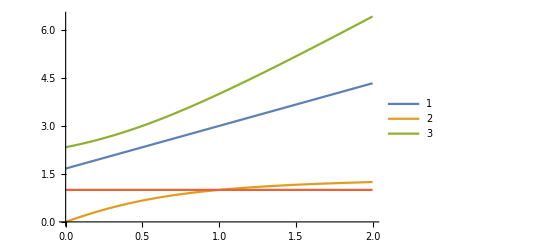

```mathematica
Plot[{1/3 (5+4 G),1/6 (7+8 G-√(49-32 G+64 G^2)),1/6 (7+8 G+√(49-32 G+64 G^2)),1},{G,0,2},PlotLegends->{"1","2","3"}]
```